# The Boundaries of the Amplituhedron 𝒜_(6,2) (m=2)

#### Load Package

```mathematica
SetDirectory[NotebookDirectory[]];
Get["amplituhedronBoundaries`"]
```

Amplituhedron Boundaries
-Graphics-
Tomasz Łukowski and Robert Moerman (2020)

-Graphics-
Grassmannian Positroids, Plabic Graphs,
& Scattering Amplitudes in N=4 SYM
Jacob L. Bourjaily, 2012

## The Boundary Stratification

#### F-vector and Euler characteristic

```mathematica
Join[{1},Reverse[List@@Counts[ampDimension/@ampStratification[topCell[6,2]]]]]
%.(-1)^Range[Length[%]]
```

{1,15,30,21,6,1}

0

#### Visualising the boundary stratification

```mathematica
ampStratificationToTable[topCell[6,2],fancyPermutations->True]
```

-Graphics- | -Graphics- | -Graphics-
4 | -Graphics-
-Graphics- | 1
3 | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 6
2 | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 21
1 | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 30
0 | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 15

```mathematica
ampStratificationToTable[topCell[6,2],fancyPermutations->True,graphicType->"lediagram"]
```

-Graphics- | -Graphics- | -Graphics-
4 | -Graphics-
+ | + | + | +
+ | + | + | + | 1
3 | -Graphics-
0 | 0 | 0 | +
+ | + | + | + | -Graphics-
+ | + | + | +
0 | 0 | 0 | + | -Graphics-
+ | + | + | +
0 | 0 | + |  | -Graphics-
+ | + | + | +
0 | + |  |  | -Graphics-
+ | + | + | +
+ |  |  |  | -Graphics-
+ | 0 | 0 | 0
+ | + | + | + | 6
2 | -Graphics-
+ | + | + | +
 |  |  |  | -Graphics-
+ | + | + | +
0 |  |  |  | -Graphics-
+ | + | + | +
0 | 0 |  |  | -Graphics-
+ | + | + | +
0 | 0 | 0 |  | -Graphics-
+ | + | + | +
0 | 0 | 0 | 0 | -Graphics-
0 | 0 | 0 | 0
+ | + | + | +
-Graphics-
+ |  |  | 
+ |  |  |  | -Graphics-
0 | + |  | 
+ |  |  |  | -Graphics-
0 | + |  | 
0 | + |  |  | -Graphics-
0 | 0 | + | 
+ |  |  |  | -Graphics-
0 | 0 | + | 
0 | + |  |  | -Graphics-
0 | 0 | + | 
0 | 0 | + | 
-Graphics-
0 | 0 | 0 | +
+ |  |  |  | -Graphics-
0 | 0 | 0 | +
0 | + |  |  | -Graphics-
0 | 0 | 0 | +
0 | 0 | + |  | -Graphics-
0 | 0 | 0 | +
0 | 0 | 0 | + | -Graphics-
+ | 0 | 0 | 0
+ |  |  |  | -Graphics-
+ | 0 | 0 | 0
0 | + |  | 
-Graphics-
+ | 0 | 0 | 0
0 | 0 | + |  | -Graphics-
+ | 0 | 0 | 0
0 | 0 | 0 | + | -Graphics-
+ | 0 | 0 | 0
+ | 0 | 0 | 0 | 21
1 | -Graphics-
+ |  |  | 
 |  |  |  | -Graphics-
+ |  |  | 
0 |  |  |  | -Graphics-
0 |  |  | 
+ |  |  |  | -Graphics-
0 | + |  | 
 |  |  |  | -Graphics-
0 | + |  | 
0 |  |  |  | -Graphics-
0 | + |  | 
0 | 0 |  | 
-Graphics-
0 | 0 |  | 
+ |  |  |  | -Graphics-
0 | 0 |  | 
0 | + |  |  | -Graphics-
0 | 0 | + | 
 |  |  |  | -Graphics-
0 | 0 | + | 
0 |  |  |  | -Graphics-
0 | 0 | + | 
0 | 0 |  |  | -Graphics-
0 | 0 | + | 
0 | 0 | 0 | 
-Graphics-
0 | 0 | 0 | 
+ |  |  |  | -Graphics-
0 | 0 | 0 | 
0 | + |  |  | -Graphics-
0 | 0 | 0 | 
0 | 0 | + |  | -Graphics-
0 | 0 | 0 | +
 |  |  |  | -Graphics-
0 | 0 | 0 | +
0 |  |  |  | -Graphics-
0 | 0 | 0 | +
0 | 0 |  | 
-Graphics-
0 | 0 | 0 | +
0 | 0 | 0 |  | -Graphics-
0 | 0 | 0 | +
0 | 0 | 0 | 0 | -Graphics-
+ | 0 | 0 | 0
 |  |  |  | -Graphics-
+ | 0 | 0 | 0
0 |  |  |  | -Graphics-
+ | 0 | 0 | 0
0 | 0 |  |  | -Graphics-
+ | 0 | 0 | 0
0 | 0 | 0 | 
-Graphics-
+ | 0 | 0 | 0
0 | 0 | 0 | 0 | -Graphics-
0 | 0 | 0 | 0
+ |  |  |  | -Graphics-
0 | 0 | 0 | 0
0 | + |  |  | -Graphics-
0 | 0 | 0 | 0
0 | 0 | + |  | -Graphics-
0 | 0 | 0 | 0
0 | 0 | 0 | + | -Graphics-
0 | 0 | 0 | 0
+ | 0 | 0 | 0 | 30
0 | -Graphics-
 |  |  | 
 |  |  |  | -Graphics-
0 |  |  | 
 |  |  |  | -Graphics-
0 |  |  | 
0 |  |  |  | -Graphics-
0 | 0 |  | 
 |  |  |  | -Graphics-
0 | 0 |  | 
0 |  |  |  | -Graphics-
0 | 0 |  | 
0 | 0 |  | 
-Graphics-
0 | 0 | 0 | 
 |  |  |  | -Graphics-
0 | 0 | 0 | 
0 |  |  |  | -Graphics-
0 | 0 | 0 | 
0 | 0 |  |  | -Graphics-
0 | 0 | 0 | 
0 | 0 | 0 |  | -Graphics-
0 | 0 | 0 | 0
 |  |  |  | -Graphics-
0 | 0 | 0 | 0
0 |  |  | 
-Graphics-
0 | 0 | 0 | 0
0 | 0 |  |  | -Graphics-
0 | 0 | 0 | 0
0 | 0 | 0 |  | -Graphics-
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 15

## Facets: co-dimension 1 boundaries

#### Finding facets

```mathematica
ampBoundary[topCell[6,2]]
```

{{3,7,4,5,6,8},{3,4,8,5,6,7},{2,4,5,9,6,7},{2,3,5,6,10,7},{2,3,4,6,7,11},{6,3,4,5,7,8}}

#### Visualising facets as 3-dimensional graphs

```mathematica
topCell[6,2]//ampBoundary//#[[-1]]&//ampStratificationTo3D
```

-Graphics3D- | 1 | → | {1, 2, 3, 4, 11, 12} | 
2 | → | {1, 2, 3, 10, 5, 12} | 
4 | → | {1, 2, 9, 4, 5, 12} | 
7 | → | {1, 8, 3, 4, 5, 12} | 
11 | → | {7, 2, 3, 4, 5, 12} | 
12 | → | {7, 2, 3, 4, 11, 6} | 
13 | → | {7, 2, 3, 10, 5, 6} | 
14 | → | {7, 2, 9, 4, 5, 6} | 
15 | → | {7, 8, 3, 4, 5, 6} |

#### Intervals between facets and their 0-dimensional boundaries

```mathematica
topCell[6,2]//ampBoundary//#[[-1]]&
%//ampStratification//Select[#,ampDimension[#]==0&]&//#[[{5,9}]]&
%//ampIntervalToHasse[%%,#]&/@#&
```

{6,3,4,5,7,8}

{{7,2,3,4,5,12},{7,8,3,4,5,6}}

{-Graphics-,-Graphics-}

#### Ridges as intersections of facets

```mathematica
<<MaTeX`
ClearAll[graphSettings,graphColour]
graphColour={0,0,205}//#/256&//RGBColor@@#&//Darker[#,0.1]&;
graphSettings["polygons"][imagesize_,vertexsize_:0.65,edgescale_:2][boundaries_]:={VertexStyle->Directive[White,EdgeForm[{graphColour,Thickness[edgescale 1.5/imagesize]}]],
VertexSize->vertexsize,
EdgeStyle->{Directive[Arrowheads[20/imagesize],graphColour,Thickness[edgescale 1.5/imagesize]]},
VertexLabels->Table[A1->Placed[{MaTeX["\{"<>ToString[boundaries[[A1]]]<>"\}",Magnification->1.3],(boundaries[[A1]]//ampPermToGraphic[#,showLabels->False]&)},{Above,Center}],{A1,boundaries//Length}]}
graphSettings["graphs"][imagesize_,vertexsize_:0.65,edgescale_:2][boundaries_]:={VertexStyle->Directive[White,EdgeForm[{graphColour,Thickness[edgescale 1.5/imagesize]}]],
VertexSize->vertexsize,
EdgeStyle->{Directive[Arrowheads[20/imagesize],graphColour,Thickness[edgescale 1.5/imagesize]]},
VertexLabels->Table[A1->Placed[{MaTeX["\{"<>ToString[boundaries[[A1]]]<>"\}",Magnification->1.3],(boundaries[[A1]]//ampStratificationTo3D[#,showPermutations->False]&)},{Above,Center}],{A1,boundaries//Length}]}
```

```mathematica
Clear[imagesize]
imagesize=1500;
ampBoundary[topCell[6,2]]//Select[ampStratification[#],ampDimension[#]≥2&]&/@#&//Flatten[#,1]&//Union;
%//Table[MemberQ[ampStratification[#[[A1]]],#[[A2]]],{A1,#//Length},{A2,#//Length}]&//Boole//AdjacencyGraph//TransitiveReductionGraph//Graph[#,GraphLayout->"SpringElectricalEmbedding",Sequence@@graphSettings["polygons"][imagesize][%],
ImageSize->imagesize]&//Rasterize
```

-Graphics-

Facets which share two ridges

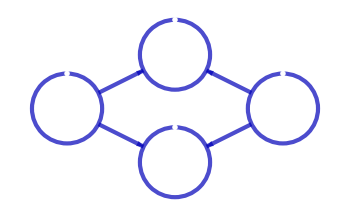

-Graphics-

```mathematica
Clear[imagesize]
imagesize=350;
ampBoundary[topCell[6,2]][[{1,2}]];
%//Select[ampStratification[#],ampDimension[#]≥2&]&/@#&//Intersection@@#&;
Union[%,%%];
%//Table[MemberQ[ampStratification[#[[A1]]],#[[A2]]],{A1,#//Length},{A2,#//Length}]&//Boole//AdjacencyGraph//TransitiveReductionGraph//Graph[#,GraphLayout->"SpringElectricalEmbedding",Sequence@@graphSettings["polygons"][imagesize][%],
ImageSize->imagesize,VertexCoordinates->{{-2,0},{2,0},{0,1},{0,-1}}]&
imagesize=1450;
%%%//Table[MemberQ[ampStratification[#[[A1]]],#[[A2]]],{A1,#//Length},{A2,#//Length}]&//Boole//AdjacencyGraph//TransitiveReductionGraph//Graph[#,GraphLayout->"SpringElectricalEmbedding",Sequence@@graphSettings["graphs"][imagesize][%%%],
ImageSize->imagesize,VertexCoordinates->{{-1,0},{1,0},{0,0.4},{0,-0.4}}]&
```

#### Facets which share only one ridge

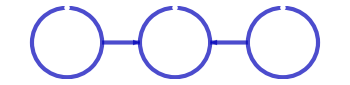

-Graphics-

```mathematica
Clear[imagesize]
imagesize=350;
ampBoundary[topCell[6,2]][[{1,3}]];
%//Select[ampStratification[#],ampDimension[#]≥2&]&/@#&//Intersection@@#&;
Union[%,%%];
%//Table[MemberQ[ampStratification[#[[A1]]],#[[A2]]],{A1,#//Length},{A2,#//Length}]&//Boole//AdjacencyGraph//TransitiveReductionGraph//Graph[#,GraphLayout->"SpringElectricalEmbedding",Sequence@@graphSettings["polygons"][imagesize][%],
ImageSize->imagesize]&
imagesize=1250;
%%%//Table[MemberQ[ampStratification[#[[A1]]],#[[A2]]],{A1,#//Length},{A2,#//Length}]&//Boole//AdjacencyGraph//TransitiveReductionGraph//Graph[#,GraphLayout->"SpringElectricalEmbedding",Sequence@@graphSettings["graphs"][imagesize][%%%],
ImageSize->imagesize]&
```

#### All ridges of a single facet as a graph

```mathematica
{6,3,4,5,7,8}//ampFacetsToGraph
```

-Graphics-